#### Algebra for thesis

The unit vectors in spherical coordinates are

```mathematica
rhat=({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}});
θhat=({{Cos[θ]Cos[ϕ]}, {Cos[θ]Sin[ϕ]}, {-Sin[θ]}});
ϕhat=({{-Sin[ϕ]}, {Cos[ϕ]}, {0}});
```

```mathematica
zhat=Cos[θ]rhat-Sin[θ]θhat;
```

```mathematica
Transpose[zhat].zhat//FullSimplify
```

{{1}}

```mathematica
zhat//FullSimplify//MatrixForm
```

(0
0
1)

```mathematica
dipole=2Cos[θ]rhat+Sin[θ]θhat;
```

```mathematica
(Transpose[zhat].dipole)[[1,1]]//FullSimplify
```

1/2 (1+3 Cos[2 θ])

```mathematica
(Transpose[dipole].dipole)[[1,1]]//FullSimplify
```

1/2 (5+3 Cos[2 θ])

```mathematica
f[θ_]:=(1+3Cos[2θ])/2
g[θ_]:=(5+3Cos[2θ])/2
```

```mathematica
(∫_0^π f[θ]Sin[θ]ⅆθ)(∫_R^∞ r^2/r^3 ⅆr)
```

Integrate::idiv: Integral of 1/r does not converge on {R,∞}.

0

```mathematica
(∫_0^π g[θ]Sin[θ]ⅆθ)(∫_R^∞ r^2/r^6 ⅆr)
```

ConditionalExpression[4/(3 R^3),Im[R]≠0||Re[R]>0]

```mathematica
Solve[(4π R^3)/3(2B0 (2μ0)/3+2M((2μ0)/3)^2)+2M((μ0 R^3)/3)^2 2π 4/(3 R^3)==0,M]
```

{{M→-B0/μ0}}

#### Minimize energy in Mathematica

```mathematica
$Assumptions:={Im[B0]==0,Im[M]==0,μ0>0,Im[θ]==0,Im[r]==0,Im[ϕ]==0,R>0}
```

The unit vectors in spherical coordinates are

```mathematica
rhat=({{Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ϕ]}, {Cos[θ]}});
θhat=({{Cos[θ]Cos[ϕ]}, {Cos[θ]Sin[ϕ]}, {-Sin[θ]}});
ϕhat=({{-Sin[ϕ]}, {Cos[ϕ]}, {0}});
```

The magnetic field inside and outside (at a position r,θ) a sphere of radius R and magnetization M is

```mathematica
Bin[M_]:=(2μ0)/3({{0}, {0}, {M}})
Bout[r_,θ_,R_,M_]:=(μ0 R^3)/(3 r^3)M(2Cos[θ]rhat+Sin[θ]θhat)
```

The total (integrated) magnetic energy inside and outside the sphere, when placed in an external constant field B_0, is proportional to (subtract the constant B_0^2 contribution)

```mathematica
Uin[R_,M_]=(4π R^3)/3(Norm[(B0({{0}, {0}, {1}})+Bin[M])]^2-B0^2)//FullSimplify
```

16/27 M π R^3 μ0 (3 B0+M μ0)

```mathematica
Uout[R_,M_]=2π∫_R^∞ (∫_0^π ((Norm[(B0({{0}, {0}, {1}})+Bout[r,θ,R,M])]^2-B0^2//Simplify))Sin[θ]ⅆθ)r^2 ⅆr
```

8/27 M^2 π R^3 μ0^2

Plot the energy as a function of M:

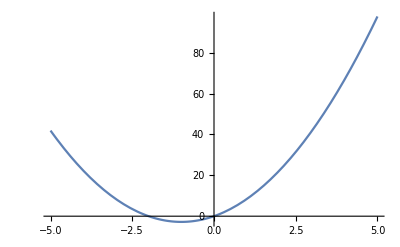

```mathematica
Plot[
(Uin[R,M]+Uout[R,M])/.{R->1,μ0->1,B0->1},
{M,-5,5}
]
```

Now solve for the M that minimizes the total energy:

```mathematica
M0=M/.Solve[D[Uin[R,M]+Uout[R,M],M]==0,M][[1,1]]
```

-B0/μ0

The field inside is therefore

```mathematica
B0+(2μ0)/3 M0
```

B0/3

#### Two shells

```mathematica
$Assumptions:={Im[B0]==0,Im[M1]==0,Im[M2]==0,μ0>0,Im[θ]==0,Im[r]==0,Im[ϕ]==0,R1>0,R2>0, R1<R2,μr≥0}
```

Now consider two concentric shells with radii R1,R2 and magnetizations M1,M2. The energy inside and outside the two shells is

```mathematica
Uin2=(4π R1^3)/3(Norm[(B0({{0}, {0}, {1}})+Bin[M1]+Bin[M2])]^2-B0^2)//FullSimplify
```

16/27 (M1+M2) π R1^3 μ0 (3 B0+(M1+M2) μ0)

```mathematica
Uout2=2π∫_R2^∞ (∫_0^π ((Norm[(B0({{0}, {0}, {1}})+Bout[r,θ,R1,M1]+Bout[r,θ,R2,M2])]^2-B0^2//Simplify))Sin[θ]ⅆθ)r^2 ⅆr
```

(8 π (M1 R1^3+M2 R2^3)^2 μ0^2)/(27 R2^3)

Between the two shells:

```mathematica
Umid2= 2π∫_R1^R2 (∫_0^π ((Norm[(B0({{0}, {0}, {1}})+Bout[r,θ,R1,M1]+Bin[M2])]^2-B0^2//Simplify))Sin[θ]ⅆθ)r^2 ⅆr
```

(8 π (-R1^3+R2^3) μ0 (M1^2 R1^3 μ0+2 M2 R2^3 (3 B0+M2 μ0)))/(27 R2^3)

Now solve for the M that minimizes the total energy, and display the field inside for each case:

```mathematica
min=Minimize[Uin2+Uout2+Umid2,{M1,M2}]//FullSimplify
(B0+(2μ0)/3 M1+(2μ0)/3 M2/.min⟦2⟧)/B0//FullSimplify
```

{-8/9 B0^2 π R2^3,{M1→0,M2→-B0/μ0}}

1/3

Introduce a linear material with relative permeability μr in the space between the two shells:

```mathematica
min=(Solve[
(D[Uin2+Uout2+ Umid2/μr,{{M1,M2}}]//FullSimplify)==0,
{M1,M2}
]//FullSimplify)[[1]]
```

{M1→(3 B0 R2^3 (-1+μr) μr)/(μ0 (2 R1^3 (-1+μr)^2-R2^3 (2+μr) (1+2 μr))),M2→(3 B0 (-R1^3 (-1+μr)^2+R2^3 (1+2 μr)))/(μ0 (2 R1^3 (-1+μr)^2-R2^3 (2+μr) (1+2 μr)))}

```mathematica
(M1/.min)/(-(3(B0/μ0)(μr-1)μr)/((2μr+1)(μr+2)-2(R1/R2)^3(μr-1)^2))//FullSimplify
```

1

```mathematica
(M2/.min)/((3(B0/μ0)((R1/R2)^3(μr-1)^2-(2μr+1)))/((2μr+1)(μr+2)-2(R1/R2)^3(μr-1)^2))//FullSimplify
```

1

The superdiamagnetic limit is:

```mathematica
Limit[M1/.min,μr->0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

```mathematica
Limit[M2/.min,μr->0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(3 B0)/(2 μ0)

The superparamagnetic limit is:

```mathematica
(Limit[M1/.min,μr->∞]/(-(3/2)/(1-(R1/R2)^3)B0/μ0))//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

```mathematica
(Limit[M2/.min,μr->∞]/((3/2)/((R2/R1)^3-1)B0/μ0))//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

```mathematica
Bin2=B0+(2μ0)/3 M1+(2μ0)/3 M2/.min//FullSimplify
```

(3 B0 R2^3 μr)/(-2 R1^3 (-1+μr)^2+R2^3 (2+μr) (1+2 μr))

```mathematica
Series[Bin2,{μr,0,2}]
```

(3 B0 R2^3 μr)/(-2 R1^3+2 R2^3)+(3 B0 R2^3 (-4 R1^3-5 R2^3) μr^2)/(4 (R1^3-R2^3)^2)+O[μr]^3

```mathematica
(3 B0 R2^3 μr)/(-2 R1^3+2 R2^3)/((3μr/2)/(1-R1^3/R2^3)B0)//FullSimplify
```

1

```mathematica
Limit[Bin2,μr->1]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

B0/3

```mathematica
Series[Bin2,{μr,∞,2}]
```

(3 B0 R2^3)/((-2 R1^3+2 R2^3) μr)+(3 B0 R2^3 (-4 R1^3-5 R2^3))/(4 (R1^3-R2^3)^2 μr^2)+O[1/μr]^3

```mathematica
(3 B0 R2^3)/((-2 R1^3+2 R2^3) μr)/((3/2)/(μr(1-R1^3/R2^3))B0)//FullSimplify
```

1

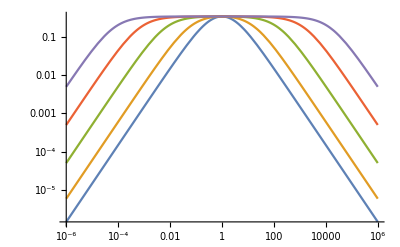

```mathematica
LogLogPlot[
{
(3 R2^3 μr)/(-2 R1^3 (-1+μr)^2+R2^3 (2+μr) (1+2 μr))/.R2->R1*100000000,
(3 R2^3 μr)/(-2 R1^3 (-1+μr)^2+R2^3 (2+μr) (1+2 μr))/.R2->R1*1.1,
(3 R2^3 μr)/(-2 R1^3 (-1+μr)^2+R2^3 (2+μr) (1+2 μr))/.R2->R1*1.01,
(3 R2^3 μr)/(-2 R1^3 (-1+μr)^2+R2^3 (2+μr) (1+2 μr))/.R2->R1*1.001,
(3 R2^3 μr)/(-2 R1^3 (-1+μr)^2+R2^3 (2+μr) (1+2 μr))/.R2->R1*1.0001
},
{μr,10^-6,10^6},
PlotRange->All
]
```

```mathematica
M1/M2/.min//FullSimplify
```

{-(R2^3 (-1+μr))/(-R1^3 (-1+μr)^2+R2^3 μr (2+μr))}

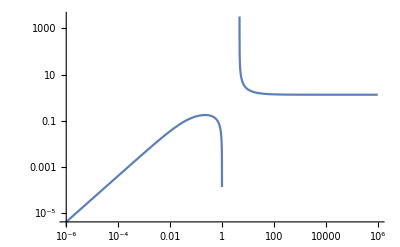

```mathematica
LogLogPlot[
-M1/M2/.min/.R2->R1*1.1,
{μr,10^-6,10^6},
PlotRange->All
]
```

```mathematica
Uin2+Uout2+ Umid2/μr
```

(8 π (M1 R1^3+M2 R2^3)^2 μ0^2)/(27 R2^3)+16/27 (M1+M2) π R1^3 μ0 (3 B0+(M1+M2) μ0)+(8 π (-R1^3+R2^3) μ0 (M1^2 R1^3 μ0+2 M2 R2^3 (3 B0+M2 μ0)))/(27 R2^3 μr)

```mathematica
Plot[
(Uin2+Uout2+ Umid2/μr),
```

$Aborted